```mathematica
FormulaGraph2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[Framed[SymbolToLabel2[ SetsToSymbol[s]],Background->White],-Pi/4],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{300,200},AspectRatio->Automatic]
]
```

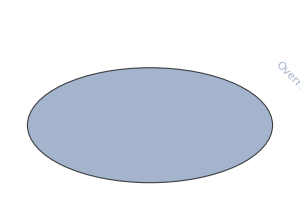
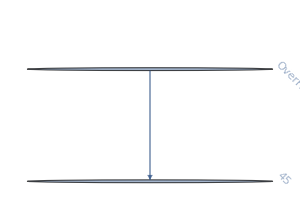
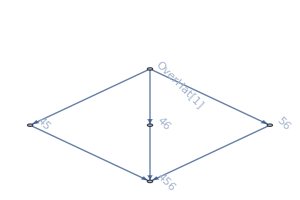
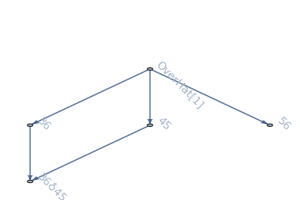
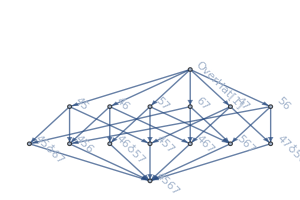
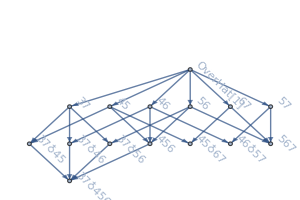
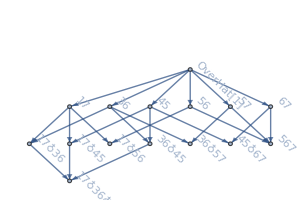
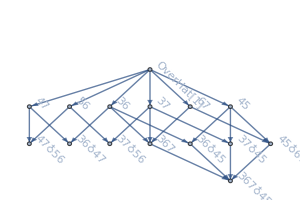
{{-Graphics-{}OverHat[1]{0,0,0,0,1}},{-Graphics-{}OverHat[1] | 45{0,0,0,0,1,1}},{-Graphics-{-Graphics-}OverHat[1] | 45 | 456
56 | 46 | {0,0,0,0,1,3,1},-Graphics-{-Graphics-}OverHat[1] | 45 | 36♁45
56 | 36 | {0,0,0,0,1,3,1}},{-Graphics-{-Graphics-,-Graphics-}OverHat[1] | 45 | 46♁57 | 457
67 | 46 | 47♁56 | 467
56 | 47 | 567 | 4567
57 | 45♁67 | 456 | {0,0,0,0,1,7,6,1},-Graphics-{-Graphics-,-Graphics-}OverHat[1] | 45 | 46♁57 | 567
67 | 46 | 37♁56 | 456
56 | 37 | 37♁45 | 37♁456
57 | 45♁67 | 37♁46 | {0,0,0,0,1,7,6,1},-Graphics-{-Graphics-,-Graphics-}OverHat[1] | 45 | 36♁57 | 17♁36
67 | 36 | 36♁45 | 567
56 | 17 | 17♁56 | 17♁36♁45
57 | 45♁67 | 17♁45 | {0,0,0,0,1,7,6,1},-Graphics-{-Graphics-,-Graphics-}OverHat[1] | 47 | 47♁56 | 37♁45
67 | 36 | 36♁45 | 367
56 | 37 | 36♁47 | 367♁45
45 | 45♁67 | 37♁56 | {0,0,0,0,1,7,6,1},-Graphics-{-Graphics-,-Graphics-}OverHat[1] | 47 | 47♁56 | 17♁45
67 | 36 | 36♁45 | 17♁36
56 | 17 | 36♁47 | 17♁36♁45
45 | 45♁67 | 17♁56 | {0,0,0,0,1,7,6,1}}}

```mathematica
Monitor[
Table[Map[With[{full=FindFullFormula[#]},
With[
{gen=FlatGenerators[full]},
Framed[
Labeled [FormulaGraph2[full],{
With[{start=CompleteGraph[VertexCount[#],GraphHighlight->EdgeList[GraphComplement[#]],VertexLabels->"Name",ImageSize->100,GraphHighlightStyle->{Red,"Thick"},VertexStyle->Red,VertexSize->Medium]},
Table[VertexDelete[start,Range[5,k]],{k,6,VertexCount[start]}]

],
Multicolumn[Map[If[MemberQ[gen,#],Framed[Style[SymbolToLabel2[#,l+3],Red],FrameStyle->Directive[Red,Dotted]],SymbolToLabel2[#,l+3]]&,Sort[full,CompareSymbols]]],
CompleteBaseCoeff[ChromaticPolynomial[#,x]]},{Left,Bottom,Top}]
]
]
]&,Map[First,Tally[CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},l],IsomorphicGraphQ[GraphComplement[#1],GraphComplement[#2]]&]]],{l,1,4}]
,l]
```